### two-photon rabi flopping

P. Huft

## global definitions

```mathematica
BuildSystem[H_,psi0_]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
]
```

## simple Rabi oscillation test

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω1,Ω2,Δ1,Δ2];
scl = 1*^9;
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies and AC stark shifts calculated in rydberg_rabi.ipynb*)
Ω1=695214755.6324366; 
Ω2 = 71550273.89520717;
ΩEff = 2π*600099;
Δ1 = -13194689145.077131;
Δ2 =-Δ1;
diffACshiftHFge =1298349.0058336519;
diffACshiftHFer=339133.4042641225;
(*Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACshiftHFge, Ω2/2}, {0, Ω2/2, (Δ1+diffACshiftHFge + Δ2 +diffACshiftHFer)}})/scl;*)
scl=1;
Ω1 = 1;Ω2=0.3;Δ1=20Ω1;Δ2=-Δ1;Γ=0;(*diagnostics, e.g. reproduce Shore examples*)

Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, Δ1+Δ2+ⅈ Γ/2}})/scl;
ΩEff = Ω1 Ω2/(2Δ1);

(*assume real Rabi freq.*)
(*scl=1;
Haf=({{0, /2, 0}, {1/2, 0, 1/2}, {0, 1/2, 0}});(*Shore, page 794 Fig. 13.3-1*)
ΩEff = 1/(2*5);*)
Haf//MatrixForm
```

(0 | 1/2 | 0
1/2 | 20 | 0.15
0 | 0.15 | 0)

Time to run sim: 0 mins

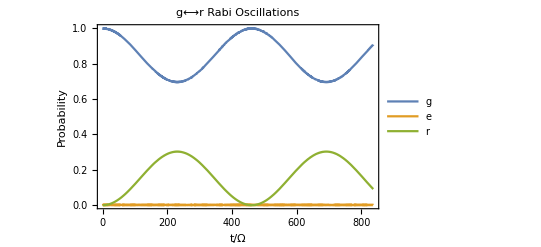

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=2π scl/ΩEff;
{ψ,sys}=BuildSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax},Method->"BDF"]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
leg = {"g","e","r"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["g⟷r Rabi Oscillations"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## frequency scan

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω1,Ω2,Δ1,Δ2];
scl = 1*^9;
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies and AC stark shifts calculated in rydberg_rabi.ipynb*)
Ω1=2π*102712885; 
Ω2 = 2π*24538455;
Δ1 = -2π*2100000000;
Δ2 =-Δ1;
ΩEff = Ω1 Ω2/(2Abs[Δ1]); 
diffACshiftHFge =1298349.0058336519;
diffACshiftHFer=339133.4042641225;
```

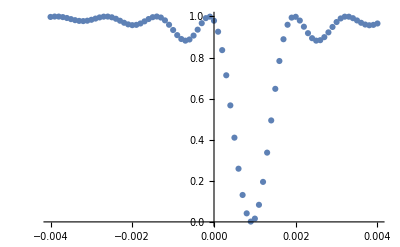

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=π scl/ΩEff;
stepmax =4;
stepmin = -4;
stepsize = .1;
steps =Range[stepmin,stepmax,stepsize];
fSteps = Table[2π fMHz*1*^6,{fMHz,steps}];
solnList = {};
endPts = {};
For[i=1, i<Length[fSteps]+1,i++,
Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACshiftHFge +fSteps[[i]], Ω2/2}, {0, Ω2/2, Δ1+diffACshiftHFge + Δ2 +diffACshiftHFer+ fSteps[[i]]}})/scl;
{ψ,sys}=BuildSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
If[Length[steps]<20,
Print[StringForm["step ``, `` mins",i,If[time>60,Floor[time/60//N],NumberForm[time/60//N,2]]]]
];
(*AppendTo[solnList, Table[soln[[j,2]],{j,Range[Length[soln]]}]];*)
AppendTo[endPts,soln[[1,2]]/.t-> tmax];
]
populationData = Transpose@{fSteps/(2π scl),Abs[endPts]^2};
ListPlot[populationData,PlotRange->{0,1}]
```

```mathematica
(Δ1+diffACshiftHFge + Δ2 +diffACshiftHFer)/(2π scl)
```

0.000260613

step 0, 0.0083 mins

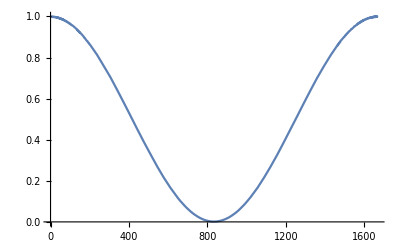

```mathematica
fRedDetuning =2π scl  Sort[populationData,#1[[2]]<#2[[2]]&][[1,1]] ;
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=2π scl/ΩEff;
Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACshiftHFge + fRedDetuning, Ω2/2}, {0, Ω2/2, Δ1+diffACshiftHFge + Δ2 +diffACshiftHFer+ fRedDetuning}})/scl;
{ψ,sys}=BuildSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["step ``, `` mins",0,If[time>60,Floor[time/60//N],NumberForm[time/60//N,2]]]]
Plot[Abs[soln[[1,2]]]^2,{t,0,tmax},PlotRange->{0,1}]
```

```mathematica
scl 2π/ΩEff//N
```

1666.39

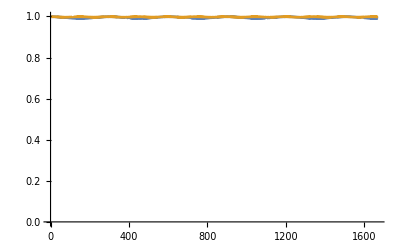

```mathematica
Plot[Evaluate[Table[Abs[solnList[[i,1]]]^2,{i,{1,Length[solnList]}}]],{t,0,tmax},PlotRange->{0,1}]
```

```mathematica
Plot[Table[Abs[solnList[[i]]]^2,{i,1,Length[solnList]}],{t,0,tmax}]
```

$Aborted

```mathematica
curves = {};
For[i=1,i<Length[solnList]+1,i++,

]
```

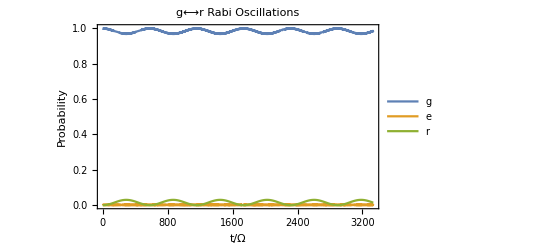

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
leg = {"g","e","r"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["g⟷r Rabi Oscillations"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
(*Export[ToString[StringForm["plot_rabi_flop_``atoms_``states_blockaded``.png",numAtoms,numStates,ΩB/Ω]],plt]*)
```